This notebook demonstrates how derangement (permutation) circuits of the Error Suppression by Derangements (ESD) [arXiv:2011.05942] and Virtual Distillation (VD) [arXiv:2011.07064] techniques can be constructed and used to suppress errors in noisy quantum devices. The approach takes n copies of a noisy quantum circuit and reduces errors exponentially as Q^n, where Q<1.

#### Definitions

Make sure to run the code below -- but don’t worry about the details, these are just definitions of the functions our demo will use

```mathematica
(* Import QuESTlink *)
Import["https://qtechtheory.org/QuESTlink.m"];
CreateDownloadedQuESTEnv[];

(* controlled SWAP operation between two full registers *)
cSWAPregs[reg1_,reg2_,qubitsperReg_,controlQB_]:=Table[
Subscript[C, controlQB][Subscript[SWAP, reg1*qubitsperReg+k,reg2*qubitsperReg+k]],{k,0,qubitsperReg-1}]

(* Derangement circuit for 2 copies *)
D2[qubitsperReg_,observable_]:= With[{controlQB=2*qubitsperReg},
Join[{Subscript[H, controlQB]},cSWAPregs[reg1=0,reg2=1,qubitsperReg,controlQB],
Circuit[Evaluate@observable]/.{Subscript[Id, n_]:>Subscript[Id, n+qubitsperReg],Subscript[O_, n_]:>Subscript[C, controlQB][Subscript[O, n+qubitsperReg]]}
,{Subscript[H, controlQB]}]
]


txt[in_]:=Text[Style[in,FontFamily->"Times New Roman",FontSize->12]]

(* Draw derangement circuit with highligting the different registers *)
DrawDerangementCircuit[derangementCirc_,numQs_,numCopies_]:=DrawCircuit[derangementCirc, 
Epilog -> Join[{
	FaceForm[None],EdgeForm[Directive[Red,Dashed]]},
Flatten@Table[
	{Text[Style[StringForm["Reg. ``",k],FontSize->12],{0,k*numQs+.4},{-1,-1}],EdgeForm[Directive[{Red,Blue}[[Mod[k,2]+1]],Dashed,Opacity[0.4]]],
	Rectangle[{0,k*numQs +.2}, {Length[derangementCirc],(k+1)numQs-.2}]},{k,0,numCopies-1}]
	]
]

(* Create n copies of a circuit -- this can be the input of the derangement circuit *)
CopiesOfCircuit[circuit_,numCopies_,qubitsperReg_]:=Flatten@Table[circuit/.{Subscript[gate_, n_]:>Subscript[gate, n+k*qubitsperReg],Subscript[gate_, n1_,n2_]:>Subscript[gate, n1+k*qubitsperReg,n2+k*qubitsperReg]},{k,0,numCopies-1}]
```

#### 1) Derangement (SWAP) circuit for two input registers

We set how many qubits there are in a register

```mathematica
numQs=5;
```

We set the observable we want to measure as products of Pauli operators (note that the ESD/VD technique suppresses errors in measuring observables)

```mathematica
observable=Product[Subscript[X, k],{k,0,numQs-1}]
```

X_0 X_1 X_2 X_3 X_4

The derangement circuit permutes the two input registers Reg. 0 and Reg. 1 and then measures the expectation value of the observable

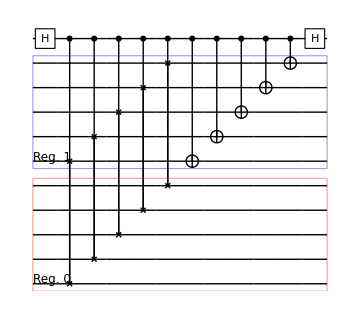

```mathematica
derangementCirc=D2[numQs,observable];
(* Draw derangement circuit and highligt the different registers *)
DrawDerangementCircuit[derangementCirc,numQs,2]
```

Total number of qubits we need to simulate (2 registers and 1 ancilla qubit)

```mathematica
totNumQ=2*numQs+1
```

11

#### 2) Mitigate errors in noisy circuits

#### Noisy circuit that generates GHZ states

Construct a noisy quantum circuit that generates an n-qubit GHZ state (|0,0,0,0,0⟩+|1,1,1,1,1⟩)/√2 with noise rate ϵ

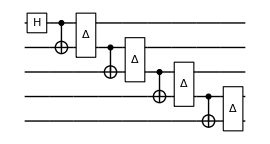

```mathematica
ϵ=0.01;
noisyGHZcirc=Join[{Subscript[H, numQs-1]},Flatten@Table[{Subscript[C, n][Subscript[X, n-1]],Subscript[Depol, n,n-1][ϵ]},{n,numQs-1,1,-1}]];
DrawCircuit[noisyGHZcirc]
```

Simulate the noisy circuit using QuESTlink

```mathematica
{ρ,ϕ}=CreateDensityQuregs[numQs,2];
ApplyCircuit[noisyGHZcirc,InitZeroState@ρ];
```

Compute the error of the expectation value ⟨X_0 X_1 X_2 X_3 X_4⟩

```mathematica
idealExpectation=1.; (* observable's known ideal expectation value is 1 *)
unmitigatedError=Abs[CalcExpecPauliSum[ρ,observable,ϕ]-idealExpectation]
```

0.0419888

#### Simulate derangement circuits: virtual distillation of 2 noisy GHZ states

Set up derangement circuit with two input GHZ circuits (for measuring the expectation value ⟨X_0 X_1 X_2 X_3 X_4⟩)

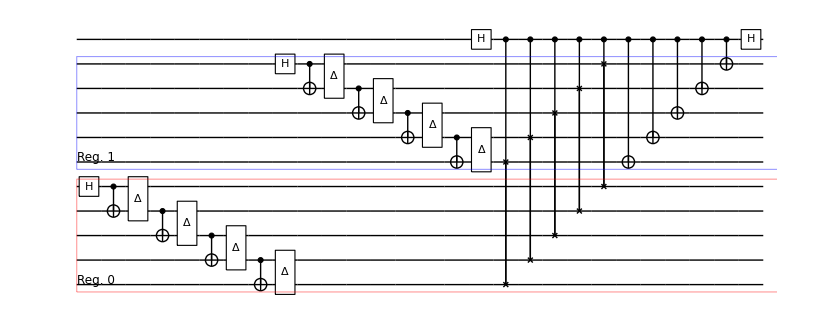

```mathematica
derangementCirc=D2[numQs,observable];
fullCirc=Join[CopiesOfCircuit[noisyGHZcirc,2,numQs],derangementCirc];
DrawDerangementCircuit[fullCirc,numQs,2]
```

Simulate the circuit in QuESTlink and compute the probability on the ancilla qubit as prob_0=Tr[ρ^2  X_0 X_1 X_2 X_3 X_4]

```mathematica
ρ=CreateDensityQureg[totNumQ];
ApplyCircuit[fullCirc,InitZeroState@ρ];
prob0=2CalcProbOfOutcome[ρ,2*numQs,0]-1;
```

Set up the circuit that measures the expectation value of the identity operator (required by the ESD/VD technique for correct normalisation)

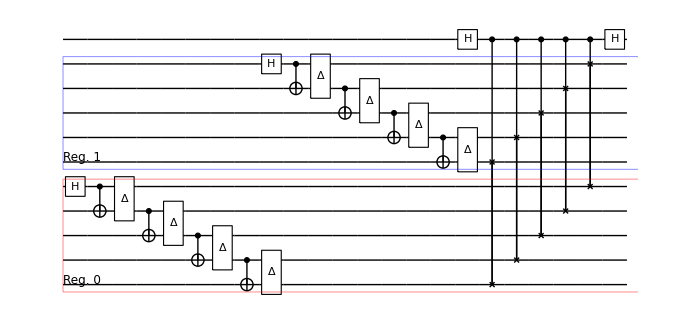

```mathematica
derangementCircId=D2[numQs,Subscript[Id, 0]];
fullCircId=Join[CopiesOfCircuit[noisyGHZcirc,2,numQs],derangementCircId];
DrawDerangementCircuit[fullCircId,numQs,2]
```

Simulate the circuit in QuESTlink and compute the probability on the ancilla qubit as prob'_0=Tr[ρ^2]

```mathematica
ApplyCircuit[fullCircId,InitZeroState@ρ];
prob0Prime=2CalcProbOfOutcome[ρ,2*numQs,0]-1;
```

The mitigated expectation value is computed via the ratio prob_0/prob'_0

```mathematica
mitigatedExp=prob0/prob0Prime
```

0.999832

Observe that the mitigated error is significantly smaller than the unmitigated one

```mathematica
errorWithDerangement=Abs[mitigatedExp-idealExpectation]
unmitigatedError
```

0.000168041

0.0419888

Try to vary the noise rate ϵ above and see how it changes the mitigated and unmitigated errors (see plot in the advanced notebook)